Define the separation requirements in time for departing aircraft.

```mathematica
incidence = {{45,68,82},
{45, 45, 68},
{45,45, 82}}
```

{{45,68,82},{45,45,68},{45,45,82}}

```mathematica
arrivalincidence= {{80,100},
{40,80}}
```

Generate some proxy data that will have interesting results.

```mathematica
weightclasses=Table[Random[Integer,{1,3}],{30}]
scheduleintervals =Table[Random[Integer, {40,80}],{29}]
```

{1,1,2,3,2,3,1,1,1,2,1,3,3,3,3,2,3,3,3,2,1,1,1,2,1,2,3,2,3,1}

{74,44,73,43,58,70,76,59,72,71,71,55,45,44,70,80,50,49,76,63,57,47,41,63,69,56,42,61,77}

Use proxy data to generate a minimal schedule, not accounting for separation constraints.

```mathematica
earliest = Table[0,{30}];
Do[earliest[[i+1]]=earliest[[i]]+scheduleintervals[[i]],{i,29}]
earliest
```

{0,74,118,191,234,292,362,438,497,569,640,711,766,811,855,925,1005,1055,1104,1180,1243,1300,1347,1388,1451,1520,1576,1618,1679,1756}

Combine the nformation above to fully specify a desired ordering of aircraft with earliest release time and weight classes.

```mathematica
initsched = Table[{i, earliest[[i]],weightclasses[[i]]},{i,30}]
```

{{1,0,1},{2,74,1},{3,118,2},{4,191,3},{5,234,2},{6,292,3},{7,362,1},{8,438,1},{9,497,1},{10,569,2},{11,640,1},{12,711,3},{13,766,3},{14,811,3},{15,855,3},{16,925,2},{17,1005,3},{18,1055,3},{19,1104,3},{20,1180,2},{21,1243,1},{22,1300,1},{23,1347,1},{24,1388,2},{25,1451,1},{26,1520,2},{27,1576,3},{28,1618,2},{29,1679,3},{30,1756,1}}

```mathematica
Fibonacci[50]
```

12586269025

Generate benchmark (original schedule, no flips)

```mathematica
dominance=Table[0,{29}]; (* Initialize data structures *)
delays = Table[0, {30}];
starts = Table[0,{30}];

 For[i=1,i<30,i++,(* Logic to sequence aircraft *)
{minsep = incidence[[initsched[[i,3]],initsched[[i+1,3]]]];If[starts[[i]]+minsep >initsched[[i+1,2]], 
{starts[[i+1]]+=minsep + starts[[i]],
dominance[[i]] = "wake"},
{starts[[i+1]]=initsched[[i+1,2]],
dominance[[i]] = "earliest"}
];
}
]
For[i = 1, i≤ 30, i++,delays[[i]]=starts[[i]]-earliest[[i]]];
makespan = starts[[30]]
delayscore = Sum[delays[[i]]^2, {i,30}]
```

1832

163682

```mathematica
score = Table[{0,0},{29}];Do[(* Wrapper to generate alternate one-flip orderings *)
{
dominance=Table[0,{29}]; (* Initialize data structures *)
delays = Table[0, {30}];
starts = Table[0,{30}];

first = initsched[[j]]; (* Implement flips *)
second =initsched[[j+1]];
permutesched = initsched;
permutesched[[j]] = second;
permutesched[[j+1]] = first;

 For[i=1,i<30,i++,(* Logic to sequence aircraft *)
{minsep = incidence[[permutesched[[i,3]],permutesched[[i+1,3]]]];If[starts[[i]]+minsep >permutesched[[i+1,2]], 
{starts[[i+1]]+=minsep + starts[[i]],
dominance[[i]] = "wake"},
{starts[[i+1]]=permutesched[[i+1,2]],
dominance[[i]] = "earliest"}
];
}
]
For[i = 1, i≤ 30, i++,delays[[i]]=starts[[i]]-earliest[[i]]];
makespan = starts[[30]],
delayscore = Sum[delays[[i]]^2, {i,30}],
(*Print["delayscore = ", delayscore," makespan = ",makespan],
*)score[[j]]= {j,makespan,delayscore};
}
,{j,29}
]

(*starts
earliest
delays
dominance
makespan*)
```

```mathematica
delays
```

{0,0,24,19,21,31,6,0,0,0,0,11,38,75,113,88,76,108,141,110,92,80,78,105,87,86,98,101,85,90}

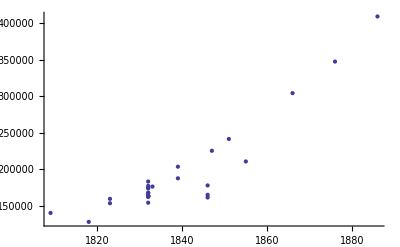

```mathematica
ListPlot[Table[Take[score[[i]],{2,3}],{i,29}]]
```

Evolutionary loop

```mathematica
paretoselect[p_]:=
{
awinners = Table[Sort[score, #1[[3]]<#2[[3]]&][[i,1]],{i,Floor[p 29]}];
bwinners = Table[Sort[score, #1[[2]]<#2[[2]]&][[i,1]],{i,Floor[p 29]}];
paretowinners = Intersection[awinners,bwinners]
}
```

```mathematica
newparents =paretoselect[.65][[1]]
```

{1,3,5,7,14,15,16,17,18,19,21,22,23,24,25,26}

```mathematica
newpop = Table[{Random[Integer, {1, Length[paretowinners]}], Random[Integer,{1,Length[paretowinners]}]},{i,10}]
```

{{1,4},{5,5},{2,2},{4,4},{7,7},{7,5},{7,2},{5,5},{5,6},{4,4}}

```mathematica
newparents
```

{18,19,21,22,24,25,26}

Loop to generate new genomes

```mathematica
ctr = 0;
newchildren = Table[{},{60}];
While[
ctr≤59, 
{try= {Random[Integer, {1, Length[newparents]}],Random[Integer,{1,Length[newparents]}]};
If[Abs[newparents[[try[[1]]]]-newparents[[try[[2]]]]]>1,
{ctr++,
newchildren[[ctr]]={newparents[[try[[1]]]],newparents[[try[[2]]]]}
}
]
}
]
```

```mathematica
newchildren
```

{{7,21},{15,18},{15,24},{23,26},{1,3},{22,17},{25,7},{19,5},{25,21},{1,19},{14,19},{21,1},{22,26},{19,24},{16,7},{19,17},{1,15},{15,22},{26,16},{7,15},{3,21},{23,16},{17,19},{24,16},{16,22},{7,5},{23,7},{18,7},{18,16},{14,17},{23,17},{19,26},{16,3},{15,24},{5,18},{3,18},{21,16},{1,21},{17,25},{16,14},{25,15},{22,14},{22,19},{18,3},{24,15},{25,19},{21,1},{1,18},{1,15},{23,18},{21,24},{18,25},{16,21},{14,24},{7,24},{7,26},{22,19},{26,14},{7,3},{23,7}}

```mathematica
newchildren[[1]]
```

```mathematica
twoflips=Union[Table[Sort[newchildren[[i]]],{i,60}]]
```

{{1,3},{1,15},{1,18},{1,19},{1,21},{3,7},{3,16},{3,18},{3,21},{5,7},{5,18},{5,19},{7,15},{7,16},{7,18},{7,21},{7,23},{7,24},{7,25},{7,26},{14,16},{14,17},{14,19},{14,22},{14,24},{14,26},{15,18},{15,22},{15,24},{15,25},{16,18},{16,21},{16,22},{16,23},{16,24},{16,26},{17,19},{17,22},{17,23},{17,25},{18,23},{18,25},{19,22},{19,24},{19,25},{19,26},{21,24},{21,25},{22,26},{23,26}}

Evaluate next generation

```mathematica
score = Table[{0,0},{29}];Do[(* Wrapper to generate alternate one-flip orderings *)
{
dominance=Table[0,{29}]; (* Initialize data structures *)
delays = Table[0, {30}];
starts = Table[0,{30}];

permutesched = initsched;(* Copy schedule to permute on *)
Do[{permutesched[[initsched[[newchildren[[j,n]]

},{n, Length[newchildren[[j]]]}
]

 For[i=1,i<30,i++,(* Logic to sequence aircraft *)
{minsep = incidence[[permutesched[[i,3]],permutesched[[i+1,3]]]];If[starts[[i]]+minsep >permutesched[[i+1,2]], 
{starts[[i+1]]+=minsep + starts[[i]],
dominance[[i]] = "wake"},
{starts[[i+1]]=permutesched[[i+1,2]],
dominance[[i]] = "earliest"}
];
}
]
For[i = 1, i≤ 30, i++,delays[[i]]=starts[[i]]-earliest[[i]]];
makespan = starts[[30]],
delayscore = Sum[delays[[i]]^2, {i,30}],
(*Print["delayscore = ", delayscore," makespan = ",makespan],
*)score[[j]]= {j,makespan,delayscore};
}
,{j,29}
]
```